```mathematica
point=(1+I)/2
```

1/2+ⅈ/2

```mathematica
1
```

1

```mathematica
point
```

1/2+ⅈ/2

```mathematica
point^2
```

ⅈ/2

```mathematica
point^3
```

-1/4+ⅈ/4

```mathematica
point^4
```

-1/4

```mathematica
point^5
```

-1/8-ⅈ/8

```mathematica
point^6
```

-ⅈ/8

```mathematica
point^7
```

1/16-ⅈ/16

```mathematica
y[n_]:={n,n^2,n^3,n^4,n^5,n^6}
```

```mathematica
y[1+I]
```

{1+ⅈ,2 ⅈ,-2+2 ⅈ,-4,-4-4 ⅈ,-8 ⅈ}

```mathematica
y[1-I]
```

{1-ⅈ,-2 ⅈ,-2-2 ⅈ,-4,-4+4 ⅈ,8 ⅈ}

```mathematica
S[n_,A_,B_]:=A(1+I)^n+B(1+I)^n
```

```mathematica
S[1,1,2]
```

3+3 ⅈ

```mathematica
(2+I)/(1-I)
```

1/2+(3 ⅈ)/2

```mathematica
A=-1;
B=1/2+(3 ⅈ)/2;
S[3,-1,1/2+(3 ⅈ)/2]
```

-2-4 ⅈ

```mathematica
Clear[A,B]
Solve[A(1+I)+B(1-I)==1&&A(1+I)^2+B(1-I)^2==]
```

{{A→-1/2-ⅈ,B→-1/2+ⅈ}}

```mathematica
S[3,-1/2-ⅈ,-1/2+ⅈ]
```

2-2 ⅈ

```mathematica
(1-I)/(1+I)
```

-ⅈ

```mathematica
(1+I)/(1-I)
```

ⅈ

```mathematica
(1-I)^6/(1-I)
```

-4+4 ⅈ

```mathematica
(1-I)^5
```

-4+4 ⅈ

```mathematica
(1+I)^20/(1-I)^20
```

1

```mathematica
I^20
```

1

```mathematica
(1+I)^2-2(1+I)+2
```

0

```mathematica
(1-I)^2-2(1-I)+2
```

0

```mathematica
(1-I)^2
```

-2 ⅈ

```mathematica
(1+I)
```

1+ⅈ

```mathematica
"convert to exponential"1+ⅈWith[{n=Abs[1+ⅈ],a=Arg[1+ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

√2 ⅇ^((ⅈ π)/4)

```mathematica
SA[n_]:=(2^(n/2)Sqrt[5]Cos[((n+4)Pi/4)+ArcTan[2]])
```

```mathematica
N@SA[{33,34,35}]
```

{65536.,262144.,393216.}

```mathematica
((-1/2)-I)
```

-1/2-ⅈ

```mathematica
"convert to exponential"-1/2-ⅈWith[{n=Abs[-1/2-ⅈ],a=Arg[-1/2-ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

1/2 √5 ⅇ^(ⅈ (-π+ArcTan[2]))

```mathematica
ArcTan[-I/(-1/2)]
```

ⅈ ArcTanh[2]

```mathematica
Norm@((-1/2)-I)
```

(√5)/2

33

```mathematica
X[θ_]:=1/(E^(I*θ)+1)^2
```

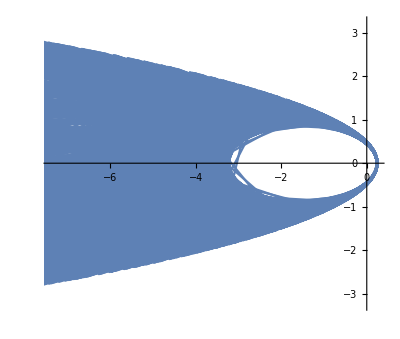

```mathematica
ParametricPlot[{Re[X[θ]],Im[X[θ]]},{θ,0,1000Pi}]
```

```mathematica
Cos[-1]-I*Sin[-1]
```

Cos[1]+ⅈ Sin[1]

```mathematica
N[Cos[1]+ⅈ Sin[1]]
```

0.540302+0.841471 ⅈ

```mathematica
z=((1/2)(1+I))
```

1/2+ⅈ/2

```mathematica
lista=Table[z^i,{i,20}]
```

{1/2+ⅈ/2,ⅈ/2,-1/4+ⅈ/4,-1/4,-1/8-ⅈ/8,-ⅈ/8,1/16-ⅈ/16,1/16,1/32+ⅈ/32,ⅈ/32,-1/64+ⅈ/64,-1/64,-1/128-ⅈ/128,-ⅈ/128,1/256-ⅈ/256,1/256,1/512+ⅈ/512,ⅈ/512,-1/1024+ⅈ/1024,-1/1024}

```mathematica
listb=Join[{0},lista]
```

{0,1/2+ⅈ/2,ⅈ/2,-1/4+ⅈ/4,-1/4,-1/8-ⅈ/8,-ⅈ/8,1/16-ⅈ/16,1/16,1/32+ⅈ/32,ⅈ/32}

```mathematica
listd=listb[[2;;Length[listb]]]
listc=listb[[1;;Length[listb]-1]]
```

{1/2+ⅈ/2,ⅈ/2,-1/4+ⅈ/4,-1/4,-1/8-ⅈ/8,-ⅈ/8,1/16-ⅈ/16,1/16,1/32+ⅈ/32,ⅈ/32}

{0,1/2+ⅈ/2,ⅈ/2,-1/4+ⅈ/4,-1/4,-1/8-ⅈ/8,-ⅈ/8,1/16-ⅈ/16,1/16,1/32+ⅈ/32}

```mathematica
liste=Thread[Join[{listc},{listd}]]
```

{{0,1/2+ⅈ/2},{1/2+ⅈ/2,ⅈ/2},{ⅈ/2,-1/4+ⅈ/4},{-1/4+ⅈ/4,-1/4},{-1/4,-1/8-ⅈ/8},{-1/8-ⅈ/8,-ⅈ/8},{-ⅈ/8,1/16-ⅈ/16},{1/16-ⅈ/16,1/16},{1/16,1/32+ⅈ/32},{1/32+ⅈ/32,ⅈ/32}}

```mathematica
ListLinePlot[liste]
```

-Graphics-

-Graphics-

```mathematica
Map[Norm,lista]
```

{1/(√2),1/2,1/(2 √2),1/4,1/(4 √2),1/8,1/(8 √2),1/16,1/(16 √2),1/32,1/(32 √2),1/64,1/(64 √2),1/128,1/(128 √2),1/256,1/(256 √2),1/512,1/(512 √2),1/1024}

```mathematica
N@%
```

{0.707107,0.5,0.353553,0.25,0.176777,0.125,0.0883883,0.0625,0.0441942,0.03125,0.0220971,0.015625,0.0110485,0.0078125,0.00552427,0.00390625,0.00276214,0.00195313,0.00138107,0.000976563}

```mathematica
Total@%
```

2.41186

```mathematica
((a+I*b)-1)/((a+I*b)-2)
```

(-1+a+b)/(-2+a+b)

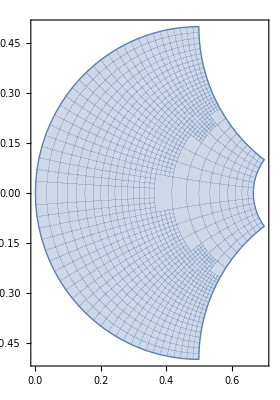

```mathematica
ParametricPlot[{Re[((a+I*b)-1)/((a+I*b)-2)],Im[((a+I*b)-1)/((a+I*b)-2)]},{a,-1,1},{b,-1,1}]
```

```mathematica
Range[-10,10,1/2]
```

{-10,-19/2,-9,-17/2,-8,-15/2,-7,-13/2,-6,-11/2,-5,-9/2,-4,-7/2,-3,-5/2,-2,-3/2,-1,-1/2,0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10}

```mathematica
Clear[y]
Solve[((1/2)+y*I-1)^10/((1/2)+y*I)^10==1,y]
```

{{y→0},{y→-√(1/4+1/(2 √5))},{y→√(1/4+1/(2 √5))},{y→-1/2 √(1/5 (5-2 √5))},{y→1/2 √(1/5 (5-2 √5))},{y→-1/2 √(5-2 √5)},{y→1/2 √(5-2 √5)},{y→-√(5/4+(√5)/2)},{y→√(5/4+(√5)/2)}}

```mathematica
Solve[((1/2)+y*I-1)^10/((1/2)+y*I-2)^10==1,y]
```

{{y→-ⅈ},{y→1/2 (-2 ⅈ-√(1/5 (5-2 √5)))},{y→1/2 (-2 ⅈ+√(1/5 (5-2 √5)))},{y→1/2 (-2 ⅈ-√(5-2 √5))},{y→1/2 (-2 ⅈ+√(5-2 √5))},{y→1/2 (-2 ⅈ-√(1/5 (5+2 √5)))},{y→1/2 (-2 ⅈ+√(1/5 (5+2 √5)))},{y→1/2 (-2 ⅈ-√(5+2 √5))},{y→1/2 (-2 ⅈ+√(5+2 √5))}}

```mathematica
Mod[1800,360]
```

0

```mathematica
-20q==1
```

```mathematica
Clear[x,y]
```

```mathematica
(x-1
```

```mathematica
1/2+I*-√(1/4+1/(2 √5))
```

1/2-ⅈ √(1/4+1/(2 √5))

```mathematica
"convert to exponential"1/2-ⅈ √(1/4+1/(2 √5))With[{n=Abs[1/2-ⅈ √(1/4+1/(2 √5))],a=Arg[1/2-ⅈ √(1/4+1/(2 √5))]},Defer[n ⅇ^(ⅈ a)]]
```

√(1/2+1/(2 √5)) ⅇ^(ⅈ (-ArcTan[2 √(1/4+1/(2 √5))]))

```mathematica
N[√(1/2+1/(2 √5)) ⅇ^(ⅈ (-ArcTan[2 √(1/4+1/(2 √5))]))]
```

0.5-0.688191 ⅈ

```mathematica
"convert to exponential"0.5-0.6881909602355868 ⅈWith[{n=Abs[0.5-0.6881909602355868 ⅈ],a=Arg[0.5-0.6881909602355868 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

0.850651 ⅇ^(ⅈ (-0.942478))

```mathematica
36*10
```

360

```mathematica
-36*10+2*360
```

360

```mathematica
18*10
```

180

```mathematica
range=Range[-72,72,18]*(Pi/180)
```

{-(2 π)/5,-(3 π)/10,-π/5,-π/10,0,π/10,π/5,(3 π)/10,(2 π)/5}

```mathematica
N@1/(2*Cos[range])
```

{1.61803,0.850651,0.618034,0.525731,0.5,0.525731,0.618034,0.850651,1.61803}

```mathematica
Clear[y]
N@Solve[((1/2)+y*I-1)^10/((1/2)+y*I)^10==1,y]
```

{{y→0.},{y→-0.688191},{y→0.688191},{y→-0.16246},{y→0.16246},{y→-0.363271},{y→0.363271},{y→-1.53884},{y→1.53884}}

```mathematica
ArcTan[1.5388417685876268/(1/2)]
```

1.25664

```mathematica
N[1.2566370614359172/°]
```

72.